# SIS with batch deaths of infected:

```mathematica
Format[k4]:=Subscript[μ,s];
Format[k3]:=Subscript[μ,i];Format[k2]:=β;
Format[k1]:=Λ;Format[k5]:=γ;
(*1: First steps*)
ClearAll["Global‘*"]
SetDirectory[NotebookDirectory[]];SetOptions[$FrontEndSession, NotebookAutoSave -> True];
NotebookSave[];
AppendTo[$Path, FileNameJoin[{$HomeDirectory, "Dropbox", "EpidCRNmodels"}]];<<EpidCRN`;
(* ?EpidCRN`**)

(*reaction Network*)
RN = { 0 -> "s",
       "s" + "i" -> 2*"i",
       k* "i" -> 0,
       "s" -> 0,
       "i" -> "s"
       };
      
cmu={k3->μ/k};{RHS, spe,Rv}=reaToRHS[RN]/.cmu;

var=ToExpression[spe];cDFE={i->0};ck1={k1-> μ  i^(k-1)(k4/k2+  i)+ k4 k5/k2,
s->(μ i^(k-1)+k5)/k2};
(*sol by hand for Λ*)
csE=s->(k3 k i^(k-1)+k5)/k2;
par=Par[RHS,var];cp=Thread[par>0];cv=Thread[var>=0];ct=Join[cp,cv];
eq=Thread[RHS==0];
eqp=Join[eq,ct];
jac=Grad[RHS,var];
Print["RHS=",RHS//MatrixForm," and jac=",jac//MatrixForm];
(*so=reCL[Solve[eq]/. Subscript[EpidCRN`Private`k, n_] :> Subscript[k, n]];
Print["there is ",so//Length," fixed pt",so]*)
sd=Solve[(RHS[[1]]/.i->0)==0,s][[1]];
Print["For k>1, DFE =", dfe=Join[sd,{i->0}]]

Print["sol by hand  valid ?",RHS/.ck1//FullSimplify]
jacD=jac/.cDFE//FullSimplify;
Print["DFE jac=",jac/.cDFE//FullSimplify//MatrixForm, " with eigv", Eigenvalues[jacD]]
jacE=jac/.ck1//FullSimplify;
Print["The eigs at DFE"]
Eigenvalues[jacD]
Print["End jac=",jacE//FullSimplify//MatrixForm,"has cofs"]
cof=CoefficientList[CharacteristicPolynomial[jacE,u],u]//FullSimplify



se=Solve[(RHS[[2]]/i)==0,s][[1]]
Print["The following polynomial wrt i endemic is of degree k "]
poli=Total[RHS/.se]//FullSimplify (*Numerator[Together[poli]]*)
Print["It admits one positive root when R0>1"]

(*expr2 = RHS[[2]] /. i^k -> i*i^(k - 1);
Collect[expr2, i]*)

(*Particular check*)
Print["The RHS admits the following fps when k=1"]
Solve[(RHS/.k->1)==0,var]//FullSimplify

Print["Minimial siphon"]
mS=minSiph[spe,asoRea[RN]]
Print["Check siphons=",isSiph[ToString/@var,asoRea[RN],%]&/@mS]
(*Find all invariant facets*)
Print["Invariant facets are:"];
iF=invFacet[RN,4]
```

RHS=(Λ+i γ-i β s-μ_s s
-i γ+i β s-i^k μ) and jac=(-i β-μ_s | γ-β s
i β | -γ+β s-i^(-1+k) k μ)

For k>1, DFE ={s→Λ/μ_s,i→0}

sol by hand  valid ?{0,0}

DFE jac=(-μ_s | γ-β s
0 | -γ+β s-0^(-1+k) k μ) with eigv{-μ_s,-γ+β s-0^(-1+k) k μ}

The eigs at DFE

{-μ_s,-γ+β s-0^(-1+k) k μ}

End jac=(-i β-μ_s | -i^(-1+k) μ
i β | -i^(-1+k) (-1+k) μ)has cofs

{i^(-1+k) (i k β+(-1+k) μ_s) μ,i β+μ_s+i^(-1+k) (-1+k) μ,1}

{s→(i γ+i^k μ)/(i β)}

The following polynomial wrt i endemic is of degree k

Λ-(i μ_s γ+i^k (i β+μ_s) μ)/(i β)

It admits one positive root when R0>1

The RHS admits the following fps when k=1

{{s→Λ/μ_s,i→0},{s→(γ+μ)/β,i→(Λ β-μ_s (γ+μ))/(β μ)}}

Minimial siphon

{{i}}

Check siphons={True}

Invariant facets are:

{{i}}

#### Computing R0 using our script:

```mathematica
mod={RHS,var,par};

inf={2};
Print["(i')=", RHS[[inf]]//MatrixForm]
jI=Grad[RHS[[inf]],var[[inf]]]; 
ng=NGM[mod,inf];K=ng[[6]];
jI=ng[[1]];
Print["Jacobian wrt infectious class :",jI//MatrixForm]
Print[" K=",K//MatrixForm," has eig"]
eig=K//Eigenvalues
R0=eig[[1]]/.dfe//FullSimplify;
Print["R0=",R0]
```

(i')=(-i γ+i β s-i^k μ)

Jacobian wrt infectious class :(-γ+β s-i^(-1+k) k μ)

K=((β s)/(γ+0^(-1+k) k μ)) has eig

{(β s)/(γ+0^(-1+k) k μ)}

R0=(Λ β)/(μ_s γ+0^(-1+k) k μ_s μ)

#### Phase-Portraits when k=1 and k>1:

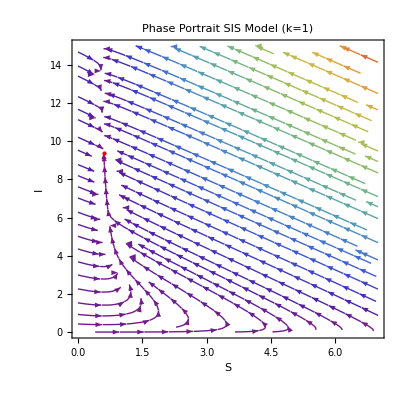

phk1.pdf

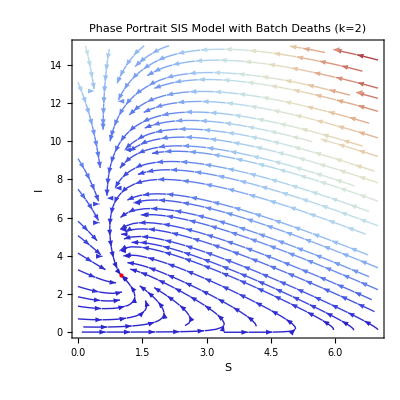

phk2.pdf

```mathematica
cn={Λ->1,β->0.5,μs->0.1,μ->0.1,γ->0.2 };
sisVectorField[k_]:=Module[{s,i},{s,i}↦{Λ-β s i-μs s+γ i,β s i-μ i^k-γ i}/. cn];

(*StreamPlot for k=1*)
ph1=StreamPlot[Evaluate[sisVectorField[1][s,i]],{s,0,7},{i,0,15},StreamStyle->Arrowheads[0.02],
StreamColorFunction->"Rainbow",StreamColorFunctionScaling->True,FrameLabel->{"S","I"},
Epilog->{Red,PointSize[Large],Point[{((γ+μ)/β/.cn),(Λ β-μs γ-μs μ)/(β μ)/.cn}]},PlotLabel->"Phase Portrait SIS Model (k=1)"]
Export["phk1.pdf",ph1]
(*StreamPlot for k=2*)
ph2=StreamPlot[Evaluate[sisVectorField[2][s,i]],{s,0,7},{i,0,15},StreamStyle->Arrowheads[0.02],
StreamColorFunction->"ThermometerColors",StreamColorFunctionScaling->True,FrameLabel->{"S","I"},
Epilog->{Red,PointSize[Large],Point[{((2 β γ-μs μ+√μ √(4 Λ β^2-4 β μs γ+μs^2 μ))/(2 β^2)/.cn),(-(μs μ)/β+(√μ √(4 Λ β^2-4 β μs γ+μs^2 μ))/β)/(2 μ)/.cn}]},
PlotLabel->"Phase Portrait SIS Model with Batch Deaths (k=2)"]
Export["phk2.pdf",ph2]
```